# Erfc NDF

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

### notation

u = m . n = Cos[θ_m]
α  = roughness

## Definitions and derivations

```mathematica
Erfc`D[u_,α_]:=Erfc[(√(1-u^2))/(α u)]/(2 α u^3 √(π-π u^2))HeavisideTheta[u]
```

```mathematica
Erfc`σ[u_,α_]:=1/4 (2 u+(ⅇ^(u^2/((-1+u^2) α^2)) √(1-u^2) α)/(√π)+2 u Erf[u/(√(1-u^2) α)]+(u^2 Gamma[0,-u^2/((-1+u^2) α^2)])/(√(π-π u^2) α))
```

```mathematica
Erfc`Λ[u_,roughness_]:=1/4 (-2 Erfc[u/(roughness √(1-u^2))]+(√(1-u^2) (ⅇ^(-u^2/(roughness^2 (1-u^2))) roughness^2+(u^2 ExpIntegralE[1,u^2/(roughness^2 (1-u^2))])/(1-u^2)))/(√π roughness u))
```

```mathematica
(1+Erfc`Λ[u,α])u==Erfc`σ[u,α]//FullSimplify
```

True

```mathematica
(Erfc`Λ[u,α])u==Erfc`σ[-u,α]//FullSimplify
```

True

```mathematica
FullSimplify[Erfc`Λ[u,u/(√(1-u^2) x)],Assumptions->0<u<1&&x>0]
```

1/4 (-2 Erfc[x]+(ⅇ^(-x^2)+x^2 ExpIntegralE[1,x^2])/(√π x))

### derivation

```mathematica
Beckmann`D[u_,α_]:=(ⅇ^(-(-1+1/u^2)/α^2))/(α^2 π u^4)HeavisideTheta[u]
```

```mathematica
Integrate[Beckmann`D[u,α m],{m,0,1},Assumptions->0<u<1&&α>0]
```

Erfc[(√(1-u^2))/(u α)]/(2 u^3 √(π-π u^2) α)

### shape invariant f(x)

```mathematica
FullSimplify[Erfc`D[u,α] u^4 α^2/.u->1/(√(1+x^2 α^2)),Assumptions->1-1/(√(1+x^2 α^2))>0&&x>0&&α>0]
```

Erfc[x]/(2 √π x)

### height field normalization

```mathematica
Integrate[2Pi u Erfc`D[u,α],{u,0,1},Assumptions->0<α<1]
```

1

### distribution of slopes

```mathematica
FullSimplify[Erfc`D[1/(√(p^2+q^2+1)),α](1/(√(p^2+q^2+1)))^4,Assumptions->0<α<1&&p>0&&q>0]
```

Erfc[(√(p^2+q^2))/α]/(2 √π √(p^2+q^2) α)

```mathematica
Erfc`P22[p_,q_,α_]:=Erfc[(√(p^2+q^2))/α]/(2 √π √(p^2+q^2) α)
```

```mathematica
Integrate[Erfc`P22[p,q,α],{p,-Infinity,Infinity},{q,-Infinity,Infinity},Assumptions->0<α<1]
```

1

### compare σ to delta integral:

```mathematica
Delta`σ[u_,ui_]:=Re[2(√(1-u^2-ui^2)+u ui ArcCos[-(u ui)/(√(1-u^2) √(1-ui^2))])]
```

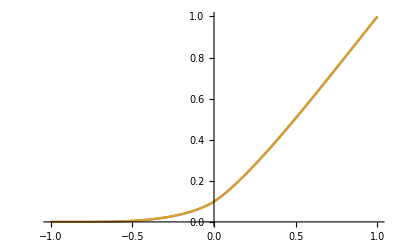

```mathematica
With[{α=.7},
Plot[{
Quiet[NIntegrate[Erfc`D[ui,α]Delta`σ[u,ui],{ui,0,1}]],
Quiet[Erfc`σ[u,α]]
},{u,-1,1}]
]
```

### importance sampling

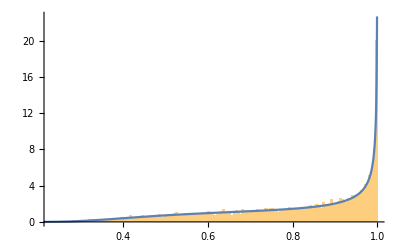

```mathematica
With[{α=1.7},
Show[
Histogram[Table[1/(√(1-(α RandomReal[])^2 (Log[RandomReal[]]))),{i,Range[10000]}],200,"PDF"],
Plot[Erfc`D[u,α]2 Pi u,{u,0,.999},PlotRange->All]
]
]
```